## One.

```mathematica
data = {{10.009, 91.0},{30.0279,2188.0},{40.0372,3372.0},{50.0465,8126.0},{60.05585,12025.0},{80.0744,18329.0},{100.093,27153.0},{120.1117,31233.0},{200.1861,37986.0},{300.279,39662.0},{1000.930,39967.0}};
data = Map[{#[[1]], #[[2]]/40000}&, data];
```

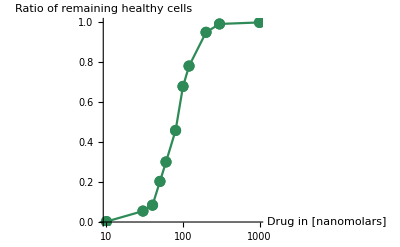

```mathematica
ListPlot[data,
AxesLabel->{"Drug in [nanomolars]","Ratio of remaining healthy cells"},
Joined->True,
Mesh->Full,
PlotStyle->Directive[ColorData["Legacy","SeaGreen"],PointSize[0.02]],
ScalingFunctions->{"Log"}
]
```

## Two.

```mathematica
raw={{39982.0,39855.0,39409.0,38384.0,36556.0,34356.0,31685.0,28990.0,25965.0,22917.0},{39981.0,39856.0,39429.0,38148.0,35510.0,31698.0,26931.0,21936.0,17063.0,12670.0},{39981.0,39778.0,38811.0,35642.0,29773.0,22085.0,14761.0,8719.0,4570.0,2350.0},{39982.0,39763.0,38547.0,34106.0,24752.0,14821.0,7116.0,2975.0,1341.0,546.0},{39982.0,39817.0,38695.0,33351.0,20856.0,8543.0,2793.0,1006.0,172.0,14.0},{39982.0,39766.0,38454.0,32062.0,15722.0,2839.0,203.0,10.0,0.0,0.0},{39983.0,39769.0,38326.0,30935.0,12331.0,1347.0,48.0,3.0,0.0,0.0},{39983.0,39693.0,37552.0,27159.0,6859.0,364.0,15.0,2.0,2.0,0.0},{39984.0,39744.0,38269.0,29930.0,8660.0,370.0,19.0,6.0,2.0,1.0}};
```

```mathematica
diffusionFunction=0.00625*Power[2,#1-1]&;
```

```mathematica
diffusionFunction[1]
```

0.00625

```mathematica
f[x_]:=0.00625*x;
```

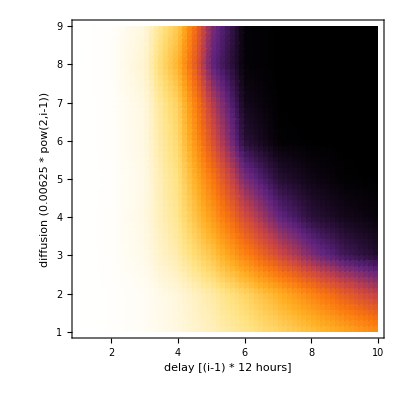

```mathematica
ListDensityPlot[raw,
Mesh->None,InterpolationOrder->1,
ColorFunction->"SunsetColors", 
Frame->True,Axes->True,
AxesLabel->{"delay [(i-1) * 12 hours]","diffusion (0.00625 * pow(2,i-1))"}]
```